```mathematica
Clear["Global`*"]
```

# Taylor Expansion

## Cory Aitchison - February 2022

Finding the coefficients that satisfy the Taylor expansion for various orders of u

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};

de[f_]:=x|->(D[f[t], {t,4}] /. t->x)+ 4 σ^4 f[x] + Γ f[x]^3;
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x]; 

ff[n_]:= x|->SubAnswers[Sum[u[k][x], {k, 0, n}], n+1];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

## Solutions

### u0

```mathematica
Solve[Series[de[ff[0]][x] == 0 /. param, {x,0,2}], {A,B}, Assumptions->{{A,B}>0}] // N
```

{{A→0.0333275,B→1.15336}}

### u0 + u1

```mathematica
Solve[Series[de[ff[1]][x] == 0 /. param, {x,0,2}], {A,B}, Assumptions->{{A,B}>0}] // N
```

{{A→0.242423,B→0.898534},{A→12.4387,B→6.26542}}

### u0 + u1 + u2 + u3

```mathematica
Solve[Series[de[ff[3]][x] == 0 /. param, {x,0,2}], {A,B}, Assumptions->{{A,B}>0}] // N
```

{{A→0.334942,B→0.69456},{A→8.87635,B→1.06939},{A→9.93573,B→14.4989}}

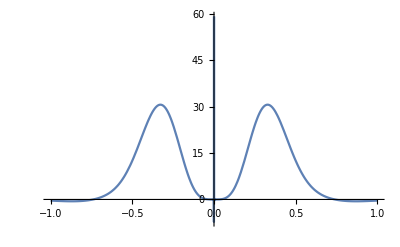

```mathematica
Plot[de[ff[3]][x] /. param /. taylorests[3], {x,-1,1}]
```